### complementary functions:

```mathematica
(* Returns number of commas in a give string expression *)
(* Has to be improved so that it ignores commas in comments *)
FindCommaPositions[thisString_?StringQ]:=StringPosition[thisString,","][[All,1]];
```

```mathematica
(* Given the current treeStructure (see explanation in errorExplorer function) and the current level, it returns the index of the last item in that level. 
Given that the expression is being processed from left to right, item is the current item *)
whatismyid[currentlevel_,thistreeStructure_]:=Module[{t=0},Print["WHAT ABOUT HERE?", KeySelect[thistreeStructure,#[[1]]==currentlevel&]];Length@KeySelect[thistreeStructure,#[[1]]==currentlevel&]];
```

```mathematica
(* Given a treeStructure (see explanation in errorExplorer function), current level in the tree, unique id, and the current function's head, 
it creates a new entry in the tree with those details & argument cound = 0 *)
newTreeEntry[level_,id_,head_,treeStructure_]:=
	{level,id+1}-> 
		Association@@
		{
			"head"-> head,
			"argnumber"-> 1,
			If[level>1,
				"parent"-> (Keys@KeySelect[treeStructure,#[[1]]==(level-1)&])[[-1]],
				"parent"->{0,0}
			],
			"pattern"-> "_"
		}
```

```mathematica
(* Returns the treeStructure, with the argument count and the pattern count of the (level,id) position both incremented *)
updateTreeEntry[level_,id_,treeStructure_]:=
	{level,id}->
		Association@@
		{
			"head"-> treeStructure[{level,id},"head"],
			"argnumber"-> treeStructure[{level,id},"argnumber"]+1,
			"parent"-> treeStructure[{level,id},"parent"],
			"pattern"-> StringJoin[treeStructure[{level,id},"pattern"],", _"]
		}
```

### Actual function

```mathematica
(* See is the main function that attempts to recreate the expression tree
It iterates the string, counts the number of arguments each function currently has and wether a bracket should be added.

Reccursion: Every time there are more than one options, the functions calls itsel with the new expression as argument in order to be tested. That is the reason,
 some of the arguments the function accepts are to describe at which stage the iteration process is.

Comments and strings are treated specially.
Arguments:
	str: The string from which the syntactically correct expressions will be created.
	treeStructure: An association of associations of the form: (level,id)-> <:head, number of arguments, parent, current pattern 
	level: corresponds to how deep in the the iteration process is currently.
	id: a unique number of each function of the same level. For example if to Cos[] functions exist at the same leve, they'll have a different id number.
	head: The head of the function currently being iterated.
*)
treeBuilder[str_?StringQ]:=
	Module[
		{
		suggestions = {},
		level = 0, 
		treeStructure = Association[<| |>], 
		head = "None",
		commasFound = 0, (* Commas correspond to arguments. Keeping track of how many commas were found, serves to know where the iteratino process is *)
		id=1,
		commaPositions = FindCommaPositions[str], (* Check where the commas are in the string. To be used with commas found. INNEFICIENT. to be improved. *)
		inComment = False, (* Keep track of whether a part of an expression is a comment, so that the contents can be ignored *)
		inString = False (* Keep track whether part of an expressino is a string, so that special characters will be ignored *)
		},
Reap[
	StringCases[ (* Iterate until some special characters are found  *)
		str,
		{
		"[":> (* Going down a level on the tree because a new function has started   *)
				(* If level ≤ 0 the current expression is wrong except if the treeStructure is empty (which corresponds to the first function call) *)
				(* The character is ignored if the flags: inComment or inString are activated *)
			Sow[If[(level > 0 || treeStructure == Association[<| |>]) && inComment ==  False && inString == False, Print["Going Down"(*,treeStructure*)];
			
			level=level+1; (* goind deeper in the expression tree  *)
			id = whatismyid[level,treeStructure]; (* figure out what the current id is *)
			treeStructure=
				Append[
				treeStructure,newTreeEntry[level,id,head,treeStructure]
				]; (* Add a new entry to the treeStructure *)
			Print["current level, id, head is: ",level," ",id, " ", head]]],
		"]" :> (* Going up one a level on the tree, because the current function has ended 
			  The character is ignored if the flags: inComment or inString are activated 
			  If level is ≤ 0, the current expression under consideration is wrong and this part is skipped  *)
			If[inComment == False && inString == False, If[level > 0, Sow[Print["Going Up"(*,treeStructure*)],
		    id = whatismyid[level,treeStructure];
			(*updateTreeEntry[level,id,treeStructure]; *)
			level--; (* Going up one level *)
			id = whatismyid[level,treeStructure];
			If[level>0,
				head=treeStructure[{level,id}][[1]],head=" "]; (* Go back to however the parent of the previus function was *)
				Print["current level, id, head is: ",level," ",id, " ", head];],level--]],
		h:LetterCharacter..:>Sow[head=h,"head"],(* Find the head of each function *)
		"," :> 
		(* Commas are the way the number of arguments in functions are infered 
		 With every comma found, an initial check whether, a closing square bracket can be positioned here, based on the number of arguments 	*)
			If[level > 0 && inComment == False && inString == False, Sow[Print["A comma was found at position ", commaPositions[[commasFound+1]]];
			id = whatismyid[level,treeStructure];
			(*matches= testPatternMatch[treeStructure,level,id];*) (* Check whether, if the current function ends here, it will be syntactically correct *)
			(*If[matches, (* If it does, branch and follow that path to the end. Append the result to the suggestions list. 
						Note: it is eventually decided that this path was not corret, the output of the function will be empty *)
				Print["Branching for: ", "]"<>StringTake[str,commaPositions[[commasFound+1]]+1;;]]; 
				suggestions = Flatten @ Append[suggestions,treeBuilder[iteratedStr<>StringTake[str,;;commaPositions[[commasFound]]],createAlternativeExpr[str,commaPositions,commasFound],"]"->Append[changes,commaPositions[[commasFound]]],treeStructure,level,id,head]]
				];*)
			commasFound++;
			treeStructure=
				Append[
					treeStructure,
					updateTreeEntry[level,id,treeStructure]
					  ]
					]],
		"(*" :> Sow[Print["Start of comment"]; inComment = True],
		"*)" :> Sow[Print["End of comment"]; inComment = False],
		"\"" :> If[inComment == False, Sow[inString = !inString]]
		}
	];,_,Rule];
	Which[
		level < 0,
			Print["We do not like that one"],
		level == 0,
			suggestions = Append[suggestions, treeStructure](*,
		level>0, suggestions = Flatten @ Append[suggestions, treeBuilder[iteratedStr <> StringTake[str,;;-1],"]",treeStructure,level,id,head]];*)
			];
	Print["End of Branching   "];
	treeStructure
]
```

### Implementation

```mathematica
(* Converting your epxressino to string *)
```

```mathematica
str="SortBy[Range[Cos[Cos[x]],Cos[x]+1], Mod[#1, 3 & ]]"
```

SortBy[Range[Cos[Cos[x]],Cos[x]+1], Mod[#1, 3 & ]]

```mathematica
result=treeBuilder[str];
```

Going Down

WHAT ABOUT HERE?<||>

current level, id, head is: 1 0 SortBy

Going Down

WHAT ABOUT HERE?<||>

current level, id, head is: 2 0 Range

Going Down

WHAT ABOUT HERE?<||>

current level, id, head is: 3 0 Cos

Going Down

WHAT ABOUT HERE?<||>

current level, id, head is: 4 0 Cos

Going Up

WHAT ABOUT HERE?<|{4,1}→<|head→Cos,argnumber→1,parent→{3,1},pattern→_|>|>

WHAT ABOUT HERE?<|{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>|>

current level, id, head is: 3 1 Cos

Going Up

WHAT ABOUT HERE?<|{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>|>

WHAT ABOUT HERE?<|{2,1}→<|head→Range,argnumber→1,parent→{1,1},pattern→_|>|>

current level, id, head is: 2 1 Range

A comma was found at position 25

WHAT ABOUT HERE?<|{2,1}→<|head→Range,argnumber→1,parent→{1,1},pattern→_|>|>

Going Down

WHAT ABOUT HERE?<|{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>|>

current level, id, head is: 3 1 Cos

Going Up

WHAT ABOUT HERE?<|{3,1}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>,{3,2}→<|head→Cos,argnumber→1,parent→{2,1},pattern→_|>|>

WHAT ABOUT HERE?<|{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>|>

current level, id, head is: 2 1 Range

Going Up

WHAT ABOUT HERE?<|{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>|>

WHAT ABOUT HERE?<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>|>

current level, id, head is: 1 1 SortBy

A comma was found at position 35

WHAT ABOUT HERE?<|{1,1}→<|head→SortBy,argnumber→1,parent→{0,0},pattern→_|>|>

Going Down

WHAT ABOUT HERE?<|{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>|>

current level, id, head is: 2 1 Mod

A comma was found at position 43

WHAT ABOUT HERE?<|{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>,{2,2}→<|head→Mod,argnumber→1,parent→{1,1},pattern→_|>|>

Going Up

WHAT ABOUT HERE?<|{2,1}→<|head→Range,argnumber→2,parent→{1,1},pattern→_, _|>,{2,2}→<|head→Mod,argnumber→2,parent→{1,1},pattern→_, _|>|>

WHAT ABOUT HERE?<|{1,1}→<|head→SortBy,argnumber→2,parent→{0,0},pattern→_, _|>|>

current level, id, head is: 1 1 SortBy

Going Up

WHAT ABOUT HERE?<|{1,1}→<|head→SortBy,argnumber→2,parent→{0,0},pattern→_, _|>|>

WHAT ABOUT HERE?<||>

current level, id, head is: 0 0

End of Branching

```mathematica
result//SortBy[#[[1]]&]//Reverse//Dataset
```

Dataset[<>]

### Visualise the result:

```mathematica
keys=Keys[result]
```

{{3,1},{4,1},{2,1},{3,2},{1,1},{2,2}}

```mathematica
names=(result//Values)[[All,"head"]]
```

{Cos,Cos,Range,Cos,SortBy,Mod}

```mathematica
forgraph=AssociationThread[keys->names]//Normal
```

{{3,1}→Cos,{4,1}→Cos,{2,1}→Range,{3,2}→Cos,{1,1}→SortBy,{2,2}→Mod}

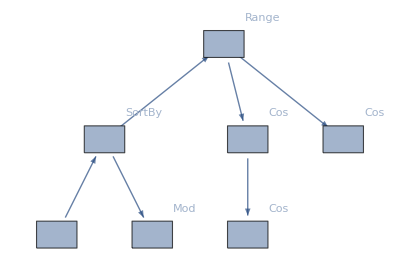

{{1,1},{2,2}}

```mathematica
mygraph=Graph[Reverse[Normal@(Lookup["parent"]/@result),2] ,VertexLabels->forgraph,VertexSize->Large,VertexShapeFunction->"Rectangle"]
```

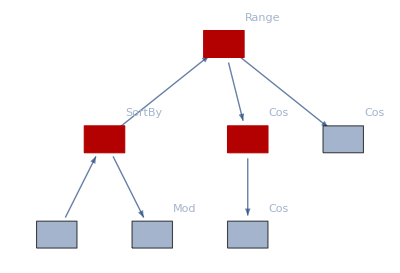

```mathematica
HighlightGraph[mygraph,FindShortestPath[mygraph,{1,1},{3,1}]]
```